```mathematica
Roots[1/(24  Λ  Ξ^2)  psimax^2 -  l0^2  Λ/(2 Ξ)  psimax + 1/Λ == 0, psimax]
```

psimax==6 (l0^2 Λ^2 Ξ-(√(-2+3 l0^4 Λ^4) Ξ)/(√3))||psimax==6 (l0^2 Λ^2 Ξ+(√(-2+3 l0^4 Λ^4) Ξ)/(√3))

```mathematica
6 l0^2 Λ^2 Ξ-(6 √(-2+3 l0^4 Λ^4) Ξ)/(√3)/.l0->L0 Ξ^(1/2)
```

6 L0^2 Λ^2 Ξ^2-2 √3 Ξ √(-2+3 L0^4 Λ^4 Ξ^2)

```mathematica
Roots[1/Λ-1/2 L0^2 psimax Λ+psimax^2/(24 Λ Ξ^2)+(L0^2 psimax^3 Λ)/(16 Ξ^2)==0,psimax]
```

psimax==-2/(9 L0^2 Λ^2)-(-4-216 L0^4 Λ^4 Ξ^2)/(18 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))+(2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)||psimax==-2/(9 L0^2 Λ^2)+((1+ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1-ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)||psimax==-2/(9 L0^2 Λ^2)+((1-ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1+ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)

```mathematica
Simplify[ComplexExpand[Re[-2/(9 L0^2 Λ^2)+((1+ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1-ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)]],Assumptions->{L0>0,Λ>0,Ξ>0}]
```

Piecewise[{{-1/(9 L0^2 Λ^2)2 (1+√(1+54 L0^4 Λ^4 Ξ^2) Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]+√(3+162 L0^4 Λ^4 Ξ^2) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]), 108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}, {(-2 (1+3078 L0^4 Λ^4 Ξ^2+1303452 L0^8 Λ^8 Ξ^4-157464 L0^12 Λ^12 Ξ^6-54 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)-43740 L0^6 Λ^6 Ξ^3 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^(1/6)-(1+54 L0^4 Λ^4 Ξ^2+(1+3078 L0^4 Λ^4 Ξ^2+1303452 L0^8 Λ^8 Ξ^4-157464 L0^12 Λ^12 Ξ^6-54 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)-43740 L0^6 Λ^6 Ξ^3 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^(1/3)) Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]-√3 (1+54 L0^4 Λ^4 Ξ^2+(1+3078 L0^4 Λ^4 Ξ^2+1303452 L0^8 Λ^8 Ξ^4-157464 L0^12 Λ^12 Ξ^6-54 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)-43740 L0^6 Λ^6 Ξ^3 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^(1/3)) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]])/(9 L0^2 Λ^2 ((1+810 L0^4 Λ^4 Ξ^2-27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))^2)^(1/6)), True}}]

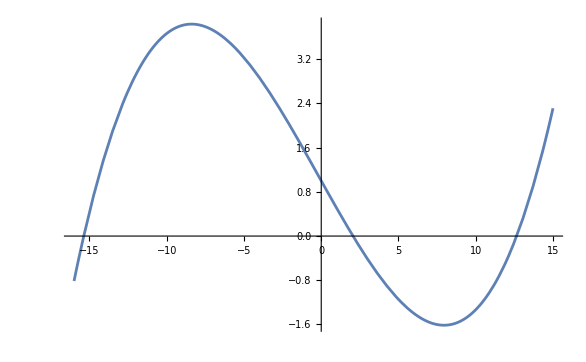

```mathematica
Plot[1-psimax/2+psimax^2/600+psimax^3/400,{psimax,-16,15}]
```

```mathematica
N[ComplexExpand[-2/(9 L0^2 Λ^2)+((1-ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1+ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)/.{L0->1,Λ-> 1, Ξ->5}]]
```

2.05767+0. ⅈ

```mathematica
ComplexExpand[-2/(9 L0^2 Λ^2)+((1-ⅈ √3) (-4-216 L0^4 Λ^4 Ξ^2))/(36 L0^2 Λ^2 (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))-((1+ⅈ √3) (-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6))^(1/3))/(9 L0^2 Λ^2)]
```

-2/(9 L0^2 Λ^2)-Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(9 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))-(6 L0^2 Λ^2 Ξ^2 Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)-1/(9 L0^2 Λ^2)Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]] ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)+Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(3 √3 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))+(6 √3 L0^2 Λ^2 Ξ^2 Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)+1/(3 √3 L0^2 Λ^2)((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]+ⅈ (Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(3 √3 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))+(6 √3 L0^2 Λ^2 Ξ^2 Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)-1/(3 √3 L0^2 Λ^2)Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]] ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)+Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(9 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))+(6 L0^2 Λ^2 Ξ^2 Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)-1/(9 L0^2 Λ^2)((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])

```mathematica
FullSimplify[(Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(3 √3 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))+(6 √3 L0^2 Λ^2 Ξ^2 Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)-1/(3 √3 L0^2 Λ^2)Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]] ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)+Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(9 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))+(6 L0^2 Λ^2 Ξ^2 Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)-1/(9 L0^2 Λ^2)((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]),Assumptions->{L0>0,Λ>0,Ξ>0}]
```

Piecewise[{{0, 108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}, {(1+54 L0^4 Λ^4 Ξ^2-(1-54 L0^2 Λ^2 Ξ (√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)+3 L0^2 Λ^2 Ξ (-19+54 L0^2 Λ^2 Ξ (-149 L0^2 Λ^2 Ξ+18 L0^6 Λ^6 Ξ^3+5 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)))))^(1/3))/(3 √3 L0^2 Λ^2 (1-54 L0^2 Λ^2 Ξ (√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)+3 L0^2 Λ^2 Ξ (-19+54 L0^2 Λ^2 Ξ (-149 L0^2 Λ^2 Ξ+18 L0^6 Λ^6 Ξ^3+5 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)))))^(1/6)), True}}]

```mathematica
FullSimplify[-2/(9 L0^2 Λ^2)-Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(9 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))-(6 L0^2 Λ^2 Ξ^2 Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)-1/(9 L0^2 Λ^2)Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]] ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)+Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]]/(3 √3 L0^2 Λ^2 ((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6))+(6 √3 L0^2 Λ^2 Ξ^2 Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]])/((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6)+1/(3 √3 L0^2 Λ^2)((-1-810 L0^4 Λ^4 Ξ^2+27 √2 ((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2)^(1/4) Cos[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]])^2+1458 √((L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)^2) Sin[1/2 Arg[L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6]]^2)^(1/6) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 √2 √(L0^4 Λ^4 Ξ^2+444 L0^8 Λ^8 Ξ^4-108 L0^12 Λ^12 Ξ^6)]],Assumptions->{L0>0,Λ>0,Ξ>0}]
```

Piecewise[{{1/(9 L0^2 Λ^2)(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]+√3 Sin[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]])), 108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}, {(54 L0^4 Λ^4 Ξ^2+(-1+(1-54 L0^2 Λ^2 Ξ (√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)+3 L0^2 Λ^2 Ξ (-19+54 L0^2 Λ^2 Ξ (-149 L0^2 Λ^2 Ξ+18 L0^6 Λ^6 Ξ^3+5 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)))))^(1/6))^2)/(9 L0^2 Λ^2 (1-54 L0^2 Λ^2 Ξ (√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)+3 L0^2 Λ^2 Ξ (-19+54 L0^2 Λ^2 Ξ (-149 L0^2 Λ^2 Ξ+18 L0^6 Λ^6 Ξ^3+5 √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)))))^(1/6)), True}}]

```mathematica
psimaxreal = FullSimplify[1/(9 L0^2 Λ^2)(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]+√3 Sin[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]])),Assumptions->{L0>0,Λ>0,Ξ>0,108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}]
```

1/(9 L0^2 Λ^2)(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]+√3 Sin[1/3 Arg[-1+27 L0^2 Λ^2 Ξ (-30 L0^2 Λ^2 Ξ+√(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))]]))

```mathematica
Simplify[Series[ psimaxreal,{Ξ,Infinity,4},Assumptions->{L0>0,Λ>0,Ξ>0,108 L0^8 Λ^8 Ξ^4>1+444 L0^4 Λ^4 Ξ^2}]]
```

1/9 (-2/(L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 ⅈ L0^2 Λ^2 Ξ √(-2-888 L0^4 Λ^4 Ξ^2+216 L0^8 Λ^8 Ξ^4)]] (-6 √6 Ξ-1/(3 (√6 L0^4 Λ^4) Ξ)+1/(648 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(18 √2 Ξ+1/(3 √2 L0^4 Λ^4 Ξ)-1/(648 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 ⅈ L0^2 Λ^2 Ξ √(-2-888 L0^4 Λ^4 Ξ^2+216 L0^8 Λ^8 Ξ^4)]])

```mathematica
N[psimaxreal/.{L0->Sqrt[85.7/100],Λ-> 1, Ξ->100}]
```

2.33393

```mathematica
Simplify[1/(9 L0^2 Λ^2)(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(-27 L0^2 Λ^2 Ξ  30 L0^2 Λ^2 Ξ+1)]]+√3 Sin[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(-27 L0^2 Λ^2 Ξ  30 L0^2 Λ^2 Ξ+1)]])),Assumptions-> {L0>0,Λ>0,Ξ>0}]
```

```mathematica
psimax2=(-2+2 √(1+54 L0^4 Λ^4 Ξ^2) (-Cos[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]+√3 Sin[1/3 ArcTan[(27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4))/(1-810 L0^4 Λ^4 Ξ^2)]]))/(9 L0^2 Λ^2)
```

```mathematica
Series[psimaxreal,{Ξ,Infinity,4},Assumptions->{Ξ>0,Λ>0,L0>0}]
```

-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-2 √(2/3) Ξ-1/(27 (√6 L0^4 Λ^4) Ξ)+1/(5832 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(2 √2 Ξ+1/(27 √2 L0^4 Λ^4 Ξ)-1/(5832 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]

```mathematica
-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-2 √(2/3) Ξ-1/(27 (√6 L0^4 Λ^4) Ξ)+1/(5832 √6 L0^8 Λ^8 Ξ^3)+O[1/Ξ]^5)+(2 √2 Ξ+1/(27 √2 L0^4 Λ^4 Ξ)-1/(5832 (√2 L0^8 Λ^8) Ξ^3)+O[1/Ξ]^5) Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]
```

```mathematica
psimaxE1=-2/(9 L0^2 Λ^2)+Cos[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]] (-(2 (√(2/3) √(L0^4 Λ^4 Ξ^2)) Ξ)/(L0^2 Λ^2 Ξ))+((2 √2 √(L0^4 Λ^4 Ξ^2) Ξ)/(L0^2 Λ^2 Ξ)){{Sin[1/3 Arg[-1-810 L0^4 Λ^4 Ξ^2+27 L0^2 Λ^2 Ξ √(2+888 L0^4 Λ^4 Ξ^2-216 L0^8 Λ^8 Ξ^4)]]}, {□}};
```

```mathematica
Expand[1/Λ-1/2 L0^2 psimax Λ+psimax^2/(24 Λ Ξ^2)+(L0^2 psimax^3 Λ)/(16 Ξ^2)/. psimax->2/(L0^2 Λ^2)+(4/(3 L0^6 Λ^6))/Ξ^2+(22/(9 L0^10 Λ^10))/Ξ^4]
```

1331/(1458 L0^28 Λ^29 Ξ^14)+121/(81 L0^24 Λ^25 Ξ^12)+803/(243 L0^20 Λ^21 Ξ^10)+232/(81 L0^16 Λ^17 Ξ^8)+161/(54 L0^12 Λ^13 Ξ^6)

```mathematica
Roots[1/Λ-1/2 L0^2 p0 Λ == 0,p0]
```

p0==2/(L0^2 Λ^2)

```mathematica
Roots[2/(3 L0^4 Λ^5 Ξ^2)-(L0^2 p2 Λ)/(2 Ξ^2)==0,p2]
```

p2==4/(3 L0^6 Λ^6)

```mathematica
Roots[11/(9 L0^8 Λ^9 Ξ^4)-(L0^2 p4 Λ)/(2 Ξ^4)==0,p4]
```

p4==22/(9 L0^10 Λ^10)

```mathematica
psimax4=2/(L0^2 Λ^2)+(4/(3 L0^6 Λ^6))/Ξ^2+(22/(9 L0^10 Λ^10))/Ξ^4;
```

```mathematica
Series[Sin[psimax4/2]Cos[psimax4/(2 Ξ)],{Ξ,Infinity,5}]
```

Sin[1/(L0^2 Λ^2)]+((2 Cos[1/(L0^2 Λ^2)])/(3 L0^6 Λ^6)-Sin[1/(L0^2 Λ^2)]/(2 L0^4 Λ^4))/Ξ^2+(64 L0^2 Λ^2 Cos[1/(L0^2 Λ^2)]-16 Sin[1/(L0^2 Λ^2)]-45 L0^4 Λ^4 Sin[1/(L0^2 Λ^2)])/(72 L0^12 Λ^12 Ξ^4)+O[1/Ξ]^6